```mathematica
Needs["FiniteFields`"]
```

```mathematica
(* pro zacatek ireducibilni polynom *)
```

Pocet chyb = rad ireducibilniho polynomu g

```mathematica
t=5;
g=GF[2,t][[2]];
```

Mnozina L = n

```mathematica
ff=GF[2,5 t]
a=ff[{0,1}]
```

GF[2,{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1}]

{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}_2

```mathematica
FieldIrreducible[ff,x]
```

1+x^22+x^25

```mathematica
PolynomialToElement[ff,1+x+x^4]
```

{1,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}_2

```mathematica
Table[AbsoluteTiming@Sum[GF[2,12][RandomInteger[{1,2},12]] x^i,{i,0,deg}]//.{x->GF[2,12][{0,1}]},{deg,12,21}]
```

{{0.036293,{0,0,0,1,0,1,1,1,1,1,0,0}_2},{0.066759,{1,0,1,0,1,0,0,0,1,0,1,0}_2},{0.142523,{0,1,0,1,0,0,0,1,0,0,0,1}_2},{0.300259,{1,1,1,0,1,1,1,0,0,1,1,0}_2},{0.63691,{0,0,1,0,0,1,1,1,1,0,1,0}_2},{1.35071,{0,0,1,0,0,0,0,0,0,0,1,1}_2},{2.86216,{1,1,1,1,0,1,0,0,1,1,1,1}_2},{6.16694,{0,0,1,0,0,0,1,0,0,0,1,0}_2},{12.5984,{1,0,0,1,1,1,1,1,0,0,1,0}_2},{27.6732,{0,0,1,0,0,0,0,0,0,0,1,0}_2}}

```mathematica
v=%;
```

{0.036293,0.066759,0.142523,0.300259,0.63691,1.35071,2.86216,6.16694,12.5984,27.6732}

-0.297859+0.0267902 2^x

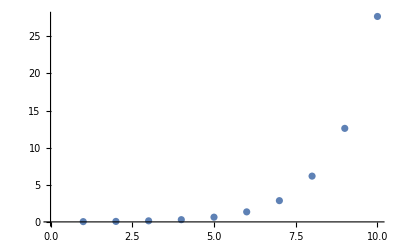

```mathematica
h=v[[All,1]]
fn=Fit[h,{1,2^x},x]
Show[
ListPlot[h],
Plot[fn,{x,0,100}]
]
```